# Global Sensitivity Analysis

## Method: Partial Rank Correlation Coefficient using Latin Hypercube Sampling (PRCC-LHS)

Author: Marisabel Rodriguez Messan, PhD

U.S. Food and Drug Administration, Silver Spring, MD 20993

This code (LHS and PRCC functions) is an adapted version (to be used in Mathematica 12.0) from the MATLAB code created by Simeone Marino.
*KirschnerLab - U Michigan Website with original MATLAB codes: http://malthus.micro.med.umich.edu/lab/usanalysis.html

To run this code (Shift+Enter to execute each cell)

## Initialization

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

## Importing Data

Melanoma patients (6 total)

```mathematica
dataNetMHCIpanAll=Import["Patients_HLA_BA.xlsx",{"XLSX","Data",1},"HeaderLines"->1];
dataNetMHCIIpanAll=Import["Patients_HLA_BA.xlsx",{"XLSX","Data",2},"HeaderLines"->1];
TcellsPatientData = Import["TcellscountsNEW.xlsx",{"XLSX","Data",1},"HeaderLines"-> 1];
ParmEstim=Import["Best-Fits.xlsx",{"XLSX","Data",1},"HeaderLines"->1];
```

### Cleaning and organizing patient data

#### Melanoma patients

Choose all rows and columns 1, 2, 8, 9

```mathematica
FullDose = TcellsPatientData[[All,{1,2,8,9}]];
```

Multiply 3rd column by 1.42857 x10^6

```mathematica
FullDoseScaleUp = FullDose/.{x_,y_,z_,w_}->{x,y,(1.42857*^6)*z,w}; (*Spot-forming cells per 10^6; there are ~1.42857x10^12 PBMCs*)
```

Group by Patients; select a specific patient

```mathematica
byPatient = GatherBy[FullDoseScaleUp,#[[2]]&];
```

```mathematica
patient1 = Select[FullDoseScaleUp,#[[2]]==1&];
patient2 = Select[FullDoseScaleUp,#[[2]]==2&];
patient3 = Select[FullDoseScaleUp,#[[2]]==3&];
patient4 = Select[FullDoseScaleUp,#[[2]]==4&];
patient5 = Select[FullDoseScaleUp,#[[2]]==5&];
patient6 = Select[FullDoseScaleUp,#[[2]]==6&];
```

## Initial tumor size estimation

Cell count (volume of a sphere, minus void volume, times 100,000)

```mathematica
Vc[d_]:=((4 Pi)/3*(d/2)^3)(0.7405)(1*^5)
```

Estimation of diameter size given cell count. Input number of cells; Output diameter in millimeters

```mathematica
Diam[cells_]:=Solve[((4 Pi)/3*(d/2)^3)(0.7405)(1*^5)==cells,d,Reals]
```

```mathematica
Diam[3.3*^8]
```

{{d→20.4172}}

```mathematica
tumorFun =Flatten[Table[NDSolve[{T'[τ]==0.004(1-T[τ]/(1.45*^10))T[τ],T[0]==t0},{T},{τ,0,180}],{t0,{851056,7.27*^8,608728,726984,500165,7.27*^8}}]];
```

```mathematica
Grid[{{Text[Style["Patient",Bold]],Text[Style["Stage by tumor\ntickness",Bold]],Text[Style["Tumor cell count\nBEFORE sugery",Bold]],Text[Style["Tumor cell count\nAFTER sugery (5%)",Bold]],Text[Style["Time lag (days)",Bold]],Text[Style["Tumor cell count\nat the beginning\nof treatment",Bold]]},
{1,Text["T3 (N3M0)"],Vc[4]+3*Vc[5],(Vc[4]+3*Vc[5])*.05,120,T[τ]/.tumorFun[[1]]/.τ->120},
{2,Text["T4 (N0M1b)"],Vc[5]+3*Vc[50],(Vc[5]+3*Vc[50])*.05,120,T[τ]/.tumorFun[[2]]/.τ->120},
{3,Text["T3 (N2M0)"],Vc[4]+2*Vc[5],(Vc[4]+2*Vc[5])*.05,165,T[τ]/.tumorFun[[3]]/.τ->165},
{4,Text["T4 (N2M0)"],Vc[5]+2*Vc[5],(Vc[5]+2*Vc[5])*.05,180,T[τ]/.tumorFun[[4]]/.τ->180},
{5,Text["T2 (N2M0)"],Vc[2]+2*Vc[5],(Vc[2]+2*Vc[5])*.05,135,T[τ]/.tumorFun[[5]]/.τ->135},
{6,Text["T2 (N0M1b)"],Vc[2]+3*Vc[50],(Vc[2]+3*Vc[50])*.05,105,T[τ]/.tumorFun[[6]]/.τ->105}},Frame->All,Background->{None,{LightBlue}},Spacings->{Automatic,.8},ItemStyle->Directive[FontSize->14],Alignment->{Center,Center}]
```

Patient | Stage by tumor
tickness | Tumor cell count
BEFORE sugery | Tumor cell count
AFTER sugery (5%) | Time lag (days) | Tumor cell count
at the beginning
of treatment
1 | T3 (N3M0) | 1.70211×10^7 | 851056. | 120 | 1.37532×10^6
2 | T4 (N0M1b) | 1.45445×10^10 | 7.27227×10^8 | 120 | 1.13968×10^9
3 | T3 (N2M0) | 1.21746×10^7 | 608728. | 165 | 1.17772×10^6
4 | T4 (N2M0) | 1.45397×10^7 | 726984. | 180 | 1.49346×10^6
5 | T2 (N2M0) | 1.00033×10^7 | 500165. | 135 | 858265.
6 | T2 (N0M1b) | 1.454×10^10 | 7.27×10^8 | 105 | 1.07825×10^9

## Latin Hypercube Sampling function

Function to create the Latin Hypercube sampling from normal and uniform distribution using method of Stein.
Note: for distrib input use “norm” for normal distribution or “unif” for uniform distribution.

```mathematica
Clear[LHCSampling]
LHCSampling[xmin_,xmean_,xmax_,xsd_,distrib_,nsample_]:=Block[{xMin=xmin,ran,idx,P,logscale,nvar,s},
If[
distrib=="norm",
ran=RandomVariate[UniformDistribution[{0,1}],nsample];
s={};
nvar=1;
(*Method of Stein*)
For[j=1,j≤nvar,j++,
idx=RandomSample[Range[nsample]];
P=(idx-ran)/nsample; (*probability of the cdf*)
AppendTo[s,xmean+Sqrt[2.]InverseErf[2.*P-1.]*xsd];
],
If[
distrib=="unif",
If[xMin==0,xMin=1.*^-3];
nvar=1;
logscale=1.*^5;
ran=RandomVariate[UniformDistribution[{0,1.}],nsample];
s={};
For[j=1,j≤nvar,j++,
idx=RandomSample[Range[nsample]];
P=(idx-ran)/nsample;
If[(xmax<1&&xMin<1)||(xmax>1&&xMin>1),
If[xmax/xMin<logscale,
AppendTo[s,xMin+P(xmax-xMin)],
AppendTo[s,Exp[Log[xMin]+P Abs[Abs[Log[xmax]]-Abs[Log[xMin]]]]];
],
If[(xmax/xMin)<logscale,
AppendTo[s,xMin+P(xmax-xMin)],
AppendTo[s,Exp[Log[xMin]+P Abs[Log[xmax]-Log[xMin]]]];
]
]
]
]
];
Flatten[s]
(*Histogram[s];*)
]
```

## Partial Rank Correlation Coefficient Function

### PRCC function for one time point of interest

The following PRCC functions calculates the partial rank correlation coefficient of the output measure of interest at one time point and parameters of interest producing this output. Additionally, it calculates the p-value for each output/parameter.
LHSmatrix: is a m x n matrix of the Latin Hypercube Sampling of each parameter. (m: # of parameters; n: sample size)
Y: is an n x k row vector (list). (n: sample size; k =1)

```mathematica
Clear[PRCC];
PRCC[LHSmatrix_,Y_,PRCCvars_,title_(*,day_*)(*,s_,alpha_*)]:=Block[{Yout,a,k,b,out,c,rnkLHSmat,rnkY,resid1,resid2,xR,zR,xs,rho,pval,LHSRank,significance},
(*PRCCvars: list of bar chart labels (x-axis labels)*)
(*Y: list of y outputs; this function reshapes this list into a column vector*)
{a,k}=Dimensions[LHSmatrix];
{b,out}=Dimensions[Y];
Yout=ArrayReshape[Y,{b,out}];(*reshapes y list into a column vector*)
rho={}; (*list of calculated ranks*)
pval={};(*list of calculated p-values*)
LHSRank={};(*matrix of ranked-parameter values*)
rnkY=Ordering[Ordering[Yout]];(*ranking of the output of interest*)
For[i=1,i≤k,i++,
rnkLHSmat=Ordering[Ordering[LHSmatrix[[All,i]]]]; (*ranking of parameter of interest*)
AppendTo[LHSRank,rnkLHSmat];
];(*ranks each column of the LHSmatrix*)
LHSRank=Transpose[LHSRank];
For[i=1,i≤k,i++,
xs=Table[x[j],{j,k-1}];(*creates a list of number of variables for linear regression model*)
xR=LHSRank[[All,i]];(*Column of parameter of interest*)
zR=Drop[LHSRank,0,{i}];(*ranking of the remaining parameters*)
resid1=LinearModelFit[Join[zR,Transpose[{xR}],2],xs,xs]["FitResiduals"];(*residuls from linear regression models of the ranked parameter of interest (xR) with respect to the other ranked parameters (zR)*)
resid2=LinearModelFit[Join[zR,Transpose[{rnkY}],2],xs,xs]["FitResiduals"];(*residuls from linear regression models of the ranked outcome measures (rnkY) with respect to the other ranked parameters (zR)*)
AppendTo[rho,Correlation[resid1,resid2]];(*save each PRCC into rho*)
AppendTo[pval,CorrelationTest[Transpose[{resid1,resid2}],0,"PearsonCorrelation",SignificanceLevel->.001]];
];
Off[CorrelationTest::nortst];
(*Add statistical significance to BarChart; *,**, or *** for alpha=0.05,0.01, or 0.001 respectively *)
asteriks={Style["★",10],Style["★★",10],Style["★★★",10]};
significance=Table[Which[.01≤ pval[[i]]<.05,Replace[pval[[i]],pval[[i]]->Flatten[asteriks[[1]]]],0.001≤ pval[[i]]<.01,Replace[pval[[i]],pval[[i]]->Flatten[asteriks[[2]]]],pval[[i]]<.001,Replace[pval[[i]],pval[[i]]->Flatten[asteriks[[3]]]],pval[[i]]≥.05,Replace[pval[[i]],pval[[i]]->" "]],{i,Length[pval]}];
labeler[v_,{r_,c_},___]:=If[v<0,Placed[significance[[c]],Below],Placed[significance[[c]],Above]];

BarChart[rho,PlotRange->{-1.01,1.01},Frame->True,ChartStyle->24(*Directive[EdgeForm[Black], 24(*Blue*)]*),FrameStyle->Directive[Black,Bold,Thickness[.003],20],ChartLabels->PRCCvars,LabelingFunction->labeler,(*ChartElementFunction->barFilled[.1,0.5,1],*)FrameLabel->{None,"PRCC Value"},PlotLabel->Style[title,Black,Bold,20],ImageSize->Large]
]
```

### PRCC function for multiple time points of interest

The following PRCC functions calculates the partial rank correlation coefficient of the output measure of interest a multiple time points and parameters of interest producing this output. This one, does not shows the p-value.

```mathematica
Clear[PRCC2];
PRCC2[LHSmatrix_,Y1_,Y2_,Y3_,PRCCvars_,title_,idx_?NumericQ,rule1_?NumericQ,rule2_?NumericQ,rule3_?NumericQ]:=Block[{Y1out,Y2out,Y3out,a,k,b,out,(*c,*)rnkLHSmat,rnkY1,rnkY2,rnkY3,resid1,resid21,resid22,resid23,xR,zR,xs,rho1,rho2,rho3,pval1,pval2,pval3,LHSRank,significance1,significance2,significance3},
(*PRCCvars: list of bar chart labels (x-axis labels)*)
(*Y: list of y outputs; this function reshapes this list into a column vector*)
{a,k}=Dimensions[LHSmatrix];
{b,out}=Dimensions[Y1];
Y1out=ArrayReshape[Y1,{b,out}];(*reshapes Y1 list into a column vector*)
Y2out=ArrayReshape[Y2,{b,out}];(*reshapes Y2 list into a column vector*)
Y3out=ArrayReshape[Y3,{b,out}];(*reshapes Y3 list into a column vector*)
rho1={}; (*list of calculated ranks*)
rho2={}; (*list of calculated ranks*)
rho3={}; (*list of calculated ranks*)
LHSRank={};(*matrix of ranked-parameter values*)
rnkY1=Ordering[Ordering[Y1out]];(*ranking of the output of interest*)
rnkY2=Ordering[Ordering[Y2out]];(*ranking of the output of interest*)
rnkY3=Ordering[Ordering[Y3out]];(*ranking of the output of interest*)
For[i=1,i≤k,i++,
rnkLHSmat=Ordering[Ordering[LHSmatrix[[All,i]]]]; (*ranking of parameter of interest*)
AppendTo[LHSRank,rnkLHSmat];
];(*ranks each column of the LHSmatrix*)
LHSRank=Transpose[LHSRank];
For[i=1,i≤k,i++,
xs=Table[x[j],{j,k-1}];(*creates a list of number of variables for linear regression model*)
xR=LHSRank[[All,i]];(*Column of parameter of interest*)
zR=Drop[LHSRank,0,{i}];(*ranking of the remaining parameters*)
resid1=LinearModelFit[Join[zR,Transpose[{xR}],2],xs,xs]["FitResiduals"];(*residuls from linear regression models of the ranked parameter of interest (xR) with respect to the other ranked parameters (zR)*)
resid21=LinearModelFit[Join[zR,Transpose[{rnkY1}],2],xs,xs]["FitResiduals"];(*residuls from linear regression models of the ranked outcome measures (rnkY) with respect to the other ranked parameters (zR)*)
resid22=LinearModelFit[Join[zR,Transpose[{rnkY2}],2],xs,xs]["FitResiduals"];(*residuls from linear regression models of the ranked outcome measures (rnkY) with respect to the other ranked parameters (zR)*)
resid23=LinearModelFit[Join[zR,Transpose[{rnkY3}],2],xs,xs]["FitResiduals"];(*residuls from linear regression models of the ranked outcome measures (rnkY) with respect to the other ranked parameters (zR)*)
AppendTo[rho1,Correlation[resid1,resid21]];(*save each PRCC into rho*)
AppendTo[rho2,Correlation[resid1,resid22]];(*save each PRCC into rho*)
AppendTo[rho3,Correlation[resid1,resid23]];(*save each PRCC into rho*)
];
Off[CorrelationTest::nortst];
BarChart[Thread[{rho1,rho2,rho3}],PlotRange->{-1.01,1.01},Frame->True,ChartStyle->{ColorData[idx][rule1],ColorData[idx][rule2],ColorData[idx][rule3]},FrameStyle->Directive[Black,Bold,Thickness[.003],22],ChartLabels->{PRCCvars,None},FrameLabel->{None,"PRCC Value"},PlotLabel->Style[title,Black,Bold,22],ImageSize->Large]
]
```

## Sensitivity Analysis methodology - PRCC/LHS

### Distribution of Estimated Parameters (frequency histograms)

The LHS/PRCC sensitivity analysis involves the repeated evaluation of the previously described deterministic model, with all of the variable values varied in each of one hundred runs (or more). The estimation uncertainty for the variables is investigated by specifying a probability density/distribution function (pdf) for each variable; hence, the variability in the pdf was used as a direct measure of the estimation uncertainty for each variable. Each specified pdf describes the range of possible values and the probability of occurrence of any specific value for the variable.
A stratified Latin Hypercube sampling scheme can be used to select the input values (the values of the variables) for each of the one hundred numerical simulations. To sample the values for each variable, each pdf is divided into 100 equi-probable intervals; consequently, the sampling distribution of the values for each variable reflects the shape of the particular pdf. Every equi-probable interval of each variable is randomly sampled 100 times, without replacement. The sampling scheme ensures that the complete range of each variable is sampled (without bias), that every equi-probable interval is used only once, and that the frequency of the selection of the possible values of each variable are determined by their probability of occurrence in the pdf. 

Calculation of the PRCCs enable the determination of the statistical relationship between each input variable and the specific output variable; these calculations assume that the relationship between each input variable and each output variable is monotonic. The PRCCs allows the independent effects of each variable to be determined, as they statistically adjusted for the variation produced by all of the other variables.

Reference
Drugs, sex and HIV: a mathematical model for New York City, Blower et al. 1991.

## ODE-model with melanoma patients’ data & parameters

### Updated Model

The function ‘VaxModelSA’ needs inputs Tt: time point (day) of interest; P: patient ID; v: vaccine ID; parameters of interest: c, c4, d, λ, T0, NTC0.

```mathematica
Clear[VaxModelSA];
VaxModelSA[Tt_?NumericQ,P_?NumericQ,v_?NumericQ,c_?NumericQ,c1_?NumericQ,d_?NumericQ,λ_?NumericQ,T0var_?NumericQ,NTC0var_?NumericQ]:= (VaxModelSA[Tt,P,v,c,c1,d,λ,T0var,NTC0var]=Module[{sol,t,pvax,Ad,Di,Dm,Ncd4,Ncd8,Acd4,Acd8,Ac,Tu,pE,MEj,ME,
pMEj,pME,pMj,pM,Mj,M,pMI,pMII,NA,injectiontimes, Dosea, Dosep,αd,αp,αpE,δM,Ka,Λ,rD,Kdc,Ktc4,Ktc8,Kt,KpM1,KpM2,a,a1,b1,b2,(*c,c1,*)c2,(*d,*)μ1,μ2,μ3,σNh,σNc,ρ1,ρ2,r,s,(*λ,*)kin,kext,kon1,kon2,koff,koffj,VE,VDC,Vsc,βM,βpM,βp,Fp1,Fp2,Vax,AffinbyPatientI,AffinbyPatientII,patientHLAAffinI ,patientHLAAffinII,KDsI,KDsII,KDeffI,KDeffII,p0,Ad0,Di0,Dm0,Ncd40,Ncd80,Acd0,Acd40,Acd80,T0,pE0,ME0,MEj0,jend,kend, n,peptide,adjuv,DCi,DCm,Ncd4p,Ncd8p,Acd4p,Acd8p,tumor,EndoPep,MEjp,MEkp,pMEjp,pMEkp,pMjp,pMkp,Mjp,Mkp(*,P,v*)},

injectiontimes = {0,3,7,14,21,83,139}; 
NA=6.0221367*^23; (*Avogadro's constant*)
Dosea=0.5*^3; (*adjuvant concentration per vaccine in mg/L*)
Dosep= {119340,120030,109570,116570,110860,111820};  (*peptide dose in pmols; Used https://www.bioinformatics.org/sms/prot_mw.html to calculate Protein Molecular weight; To convert from weight to moles: http://molbiol.edu.ru/eng/scripts/01_04.html*)
αp=0.28;αd=.5;αpE=70;Fp1={0.006,0.001,0.001,0.001,0.003,0.001};Fp2={0.007,0.002,0.006,0.002,0.002,0.001};a=5.*^7;a1=1.*^3;c2=6.5*^-11;s=0.0839;(*c1=0.835;*)

Λ=3.75;(*0.363;*)
δM=.33;(*Immature (.09) and mature DC death rate*)
rD=2.48;(*1.12;*) (*max maturation rate - DCs (see DC maturation section below-fitted)*)
Ka=6.64;(*4;*) (*mg/L - adjuvant concentration at which immature Dc activation rate is 50% max; value from fitting (see DC maturation section below) *)
Kdc=2.38*^7;  (*DC Carrying capacity; Unit: # cells *)

b1=0.15;b2=0.12;ρ1=0.0265;ρ2=0.0509;
Ktc4= (8.57*^11)*0.7;  (*T-Cells Carrying capacity; Unit: # cells*)
Ktc8=(8.57*^11)*0.3;  (*CD8 T-Cells Carrying capacity; Unit: # cells *)
μ1=0.031;μ2=0.022;
μ3=0.0029;
(*ρ1=1.51;ρ2=2.6;*)(*1*^-5;*)
σNc=3;σNh=1.5;
KpM1=400;KpM2=400;

Kt=1.45*^10; (*Tumor Carrying capacity Unit: # cells *)
r=0.004;(*0.006;*)(*d1=4.98*^-7;d2=5.1*^-7;*)
(*d1=0.17;d2= 0.1;λ=3;s1=50;s2=50;*)

βp=14.4;
βM=1.663;
βpM=.1663;
VDC=2.5388*^-12; (*https://link.springer.com/article/10.1007/s10928-013-9328-y/tables/2*)
Vsc=4*0.1919;(*;2.75;*)
VE=1*^-14;

(*Input data*)
Vax={3;;15,16;;32,33;;46,47;;60,61;;80,81;;100}; (*6 vaccines, selecting columns that correspond to each vaccine*)
AffinbyPatientI = Select[dataNetMHCIpanAll,#[[1]]==P&]; (*set of HLA's by patient - these are in rows *)
AffinbyPatientII=Select[dataNetMHCIIpanAll,#[[1]]==P&];

(*MHC I molecules*)
	   KDsI=AffinbyPatientI[[1;;,Vax[[v]]]];(* Calculate KDs for each vaccine and each HLA allotype specific to the patient*)
KDeffI=1/Total[1/Transpose[KDsI]]*1.*^3;(*pmol*)
kon1=1.8144*^-2;
koffj=kon1*KDeffI;

(*MHC II molecules*)
KDsII=AffinbyPatientII[[1;;,Vax[[v]]]];  (* Calculate KDs for each column representing an HLA allotype specific to the patient*)
KDeffII=1/Total[1/Transpose[KDsII]]*1.*^3; (*pmol*) (*list of KDeffs*)
kon2=8.64*^-3;
koff=kon2*KDeffII; (*list of kOFFs*)

(*MHC I & II molecules*)
kin=14.4;
kext=28.8;
jend=Length[AffinbyPatientI]; (*Define total number of j and k alleles for each patient; j is for alleles in MHC-I and k for alleles in MHC-II*)
kend=Length[AffinbyPatientII]; 
n=jend+kend;

(*INITIAL CONDITIONS*)
p0=0;
Ad0=0;
Di0=1*^7;
Dm0=0;
Ncd40=(5.38*^9)*.7;
Ncd80=(5.38*^9)*.3;
Acd0={patient1[[1,3]],patient2[[1,3]],patient3[[1,3]],patient4[[1,3]],patient5[[1,3]],patient6[[1,3]]};
(*Acd40={patient1[[1,3]],patient2[[1,3]],patient3[[1,3]],patient4[[1,3]],patient5[[1,3]],patient6[[1,3]]}*.7;
Acd80={patient1[[1,3]],patient2[[1,3]],patient3[[1,3]],patient4[[1,3]],patient5[[1,3]],patient6[[1,3]]}*.3;*)
T0={T[τ]/.tumorFun[[1]]/.τ->120,T[τ]/.tumorFun[[2]]/.τ->120,T[τ]/.tumorFun[[3]]/.τ->165,T[τ]/.tumorFun[[4]]/.τ->180,T[τ]/.tumorFun[[5]]/.τ->135,T[τ]/.tumorFun[[6]]/.τ->105};
pE0=0;
MEj0={40*^4/2,40*^4/2,20*^4/2,70*^4/2}/NA*1*^12;
ME0={20*^4/2,20*^4/2,10*^4/2,10*^4/2}/NA*1*^12;

pMI = NA* 1*^-12 Sum[pMj[j][t],{j,jend}];
pMII =NA *1*^-12Sum[pM[k][t],{k,kend}];

sol=NDSolve[Flatten[{
pvax'[t]==-αp pvax[t], (*Peptides in a Vaccine*)
Ad'[t]==-αd Ad[t], (*Adjuvant in a Vaccine*)
Di'[t]== Λ Di[t](1-Di[t]/Kdc)-rD(Ad[t]/(Ka+Ad[t]))Di[t],(*Immature DC*)
Dm'[t]==rD(Ad[t]/(Ka+Ad[t]))Di[t] -δM Dm[t],(*Mature Dc*)
Ncd4'[t]==b1 Ncd4[t](1-Ncd4[t]/Ktc4)-μ3 Ncd4[t]-σNh Ncd4[t]Fp1[[P]](Dm[t]/(Dm[t]+Fp1[[P]]Ncd4[t]+Acd4[t]))(pMII/(pMII+KpM2)),(*Naive CD4*)
Acd4'[t]==c1 (Tu[t]/(a1+Tu[t])) Acd4[t]+σNh Ncd4[t]Fp1[[P]](Dm[t]/(Dm[t]+Fp1[[P]] Ncd4[t]+Acd4[t]))(pMII/(pMII+KpM2))+ρ1 (Dm[t]/(Dm[t]+Fp1[[P]] Ncd4[t]+Acd4[t]))((pMII-KpM2)/(pMII+KpM2))  Acd4[t]-μ1 Acd4[t],(*Active CD4*)

Ncd8'[t]==b2 Ncd8[t](1-Ncd8[t]/Ktc8)-μ3 Ncd8[t]-σNc Ncd8[t]Fp2[[P]](Dm[t]/(Dm[t]+Fp2[[P]] Ncd8[t]+Acd8[t]))(pMI/(pMI+KpM1)),(*Naive CD8*)
Acd8'[t]==c(((d(Acd8[t]/Tu[t])^λ/(s +(Acd8[t]/Tu[t])^λ))^2 Tu[t]^2)/(a+(d(Acd8[t]/Tu[t])^λ/(s +(Acd8[t]/Tu[t])^λ))^2 Tu[t]^2)) Acd8[t]+c2 Acd4[t]Tu[t]+σNc Ncd8[t]Fp2[[P]](Dm[t]/(Dm[t]+Fp2[[P]] Ncd8[t]+Acd8[t]))*(pMI/(pMI+KpM1))+ρ2(Dm[t]/(Dm[t]+Fp2[[P]] Ncd8[t]+Acd8[t]))((pMI-KpM1)/(pMI+KpM1))  Acd8[t]-μ2 Acd8[t],(*Active CD8*)
Ac'[t]== Acd4'[t]+Acd8'[t],
Tu'[t]==r(1-Tu[t]/Kt)Tu[t]-(d(Acd8[t]/Tu[t])^λ/(s +(Acd8[t]/Tu[t])^λ))Tu[t] ,(*Tumor cells*)
(* neo-peptides *)
pE'[t]==αpE pvax[t] VE/Vsc-βp pE[t]-pE[t] (Sum[ kon1/VE MEj[j][t],{j,jend}]+Sum[kon2/VE ME[k][t],{k,kend}])+Sum[koffj [[j]]*pMEj[j][t],{j,jend}]+Sum[koff[[k]]* pME[k][t],{k,kend}],
(* MHCI and MHCII molecules in endosome *)
Table[MEj[j]'[t]==βM(MEj0[[j]]-MEj[j][t])-kon1/VE pE[t]MEj[j][t]+koffj[[j]]* pMEj[j][t]+kin Mj[j][t],{j,jend}],
Table[ME[k]'[t]==βM(ME0[[k]]-ME[k][t])-kon2/VE  pE[t] ME[k][t]+koff[[k]]* pME[k][t]+kin M[k][t],{k,kend}],
(* p-MHCI and p-MHCII complex in endosome *)
Table[pMEj[j]'[t]==kon1/VE pE[t]MEj[j][t]-(koffj[[j]]+βpM+kext)pMEj[j][t],{j,jend}],
Table[pME[k]'[t]==kon2/VE  pE[t]ME[k][t]-(koff[[k]]+βpM+kext)pME[k][t],{k,kend}],
(* p-MHCI and p-MHCII complex in DC membrane *)
Table[pMj[j]'[t]== kext pMEj[j][t]-koffj[[j]]*pMj[j][t],{j,jend}],
Table[pM[k]'[t]== kext pME[k][t]-koff[[k]]*pM[k][t],{k,kend}],
(*Free MHC I and MHC II (j, k) *)
Table[Mj[j]'[t]==koffj [[j]]*pMj[j][t]-kin Mj[j][t],{j,jend}],
Table[M[k]'[t]== koff[[k]]* pM[k][t]-kin M[k][t],{k,kend}],
Flatten[{
pvax[0]==Dosep[[P]],
Ad[0]==Dosea,
Di[0]==Di0,
Dm[0]==Dm0, 
Ncd4[0]==Ncd40,
Ncd8[0]==Ncd80,
Acd4[0]==.7*Acd0[[P]],
Acd8[0]==.3*Acd0[[P]],
Ac[0]==Acd0[[P]],
(*Tu[0]==T0,*)
Tu[0]==T0[[P]],
pE[0]==pE0,
Table[MEj[j][0]==MEj0[[j]],{j,jend}],
Table[ME[k][0]==ME0[[k]],{k,kend}],
Table[pMEj[j][0]==0,{j,jend}],
Table[pME[k][0]==0,{k,kend}],
Table[pMj[j][0]==0,{j,jend}],
Table[pM[k][0]==0,{k,kend}],
Table[Mj[j][0]==0,{j,jend}],
Table[M[k][0]==0,{k,kend}]
}], 
WhenEvent[{t==3,t==7,t==14,t==21,t==83,t==139},{pvax[t]->pvax[t]+ Dosep[[P]],Ad[t]->Ad[t]+Dosea}]
}],
Flatten[{pvax,Ad,Di,Dm,Ncd4,Ncd8,Acd4,Acd8,Ac,Tu,pE,Table[MEj[j],{j,jend}],Table[ME[k],{k,kend}],
Table[pMEj[j],{j,jend}],Table[pME[k],{k,kend}],Table[pMj[j],{j,jend}],Table[pM[k],{k,kend}],Table[Mj[j],{j,jend}],Table[M[k],{k,kend}]}],
{t,0,300},Method->StiffnessSwitching,MaxSteps->50000];
Flatten[{Ac[Tt],Tu[Tt]}/.sol]
])
```

### LH Sampling of parameters

RUN: Estimated parameters from two clinical studies (melanoma & glioblastoma); Means; Standard deviations

```mathematica
cPar= ParmEstim[[1,2;;]];
c4Par= ParmEstim[[2,2;;]];
dPar= ParmEstim[[3,2;;]];
lambdaPar =ParmEstim[[4,2;;]];
T0Par ={1.375*^6,1.139*^9,1.177*^6,1.492*^6,858265,1.078*^9};

(*Set parameter baselines (means from data)*)
cb =Mean[cPar];
c4b=Mean[c4Par];
db =Mean[dPar];
λb=Mean[lambdaPar];
T0b=Mean[T0Par];
NTC0b=5.38*^9;


(*Standard Deviations*)
csd =cb*.15;
dsd =db*.15;
c4sd=c4b*.15;
λsd=λb*.15;
T0sd=T0b*.15;
NTC0sd=(5.38*^9)*.15;
```

Sampling

```mathematica
Clear[cLHS,c4LHS,dLHS,λLHS,T0LHS,NTC0LHS,Ns,TumorY,LHSMatrix]
```

```mathematica
Ns=1000;  (*sample size*) 
cLHS =LHCSampling[Min[cPar],cb,Max[cPar],csd,"unif",Ns];
c4LHS =LHCSampling[Min[c4Par],c4b,Max[c4Par],c4sd,"unif",Ns];
dLHS =LHCSampling[Min[dPar],db,Max[dPar],dsd,"unif",Ns];
λLHS =LHCSampling[Min[lambdaPar],λb,Max[lambdaPar],λsd,"unif",Ns];
T0LHS=LHCSampling[Min[T0Par],T0b,Max[T0Par],T0sd,"unif",Ns];
NTC0LHS =LHCSampling[2.15*^9,NTC0b,8.6*^9,NTC0sd,"unif",Ns];
```

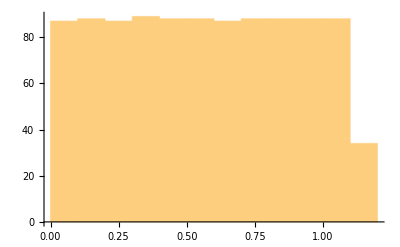

```mathematica
Histogram[T0LHS]
```

### PRCC for one time point of interest

Define LHS Matrix

```mathematica
LHSMatrix =Transpose[{cLHS,c4LHS,dLHS,λLHS,T0LHS,NTC0LHS}];
Dimensions[LHSMatrix]
```

{1000,6}

Compute model output of interest (Y-vector). The following line is to test the output. The first element of the list is the number of activated T cells and the second element is the number of tumor cells, both on day 100 for Patient ID 1 with vaccine ID 1, and using the parameter values of interest sampled on the LHS matrix (first row)

```mathematica
VaxModelSA[100,1,1,LHSMatrix[[10,1]],LHSMatrix[[10,2]],LHSMatrix[[10,3]],LHSMatrix[[10,4]],LHSMatrix[[10,5]],LHSMatrix[[10,6]]]
```

{4.57156×10^8,37398.6}

The following function calculates the model outputs (activated T cell counts and tumor cell counts) on the specified day T, patient ID P, vaccine ID V, with LHS matrix length lhsLength. The last element j can be either 1 or 2, and it specifies the position of the output in the list, e.g., 1 is activated T cells and 2 is for tumor cell counts.

```mathematica
Clear[Yvec]
Yvec[T_,P_,V_,lhsLength_,j_]:=Yvec[T,P,V,lhsLength,j]=(Reap[Do[
Sow[{Quiet[Check[VaxModelSA[T,P,V,LHSMatrix[[i,1]],LHSMatrix[[i,2]],LHSMatrix[[i,3]],LHSMatrix[[i,4]],LHSMatrix[[i,5]],LHSMatrix[[i,6]]][[j]],Continue[],{Power::infy,NDSolve::ndnum,NDSolve::ndsz,NDSolve::mxst}]]}],{i,1,lhsLength}
]][[2]])
```

The following lines are to select colors and create figure labels.

```mathematica
SwatchLegend[{ColorData[24][4],ColorData[24][5],ColorData[24][6]},{Style["Day 22 ",23],Style["Day 112 ",23],Style[ "Day 147 ",23]},LegendMarkerSize->20,LegendLayout->"Row"]
```

```mathematica
SwatchLegend[{ColorData[55][7],ColorData[55][9],ColorData[55][10]},{Style["Day 22 ",23],Style["Day 112 ",23],Style[ "Day 147 ",23]},LegendMarkerSize->20,LegendLayout->"Row"]
```

Calculate PRCCs for each patient.

#### Patient 1

```mathematica
Clear[ATCY24,tumorY1]
```

```mathematica
AbsoluteTiming[
Do[Export[ToString[i]<>"P1SAs.mx",{Flatten[Transpose[Yvec[i,1,1,1000.,1]],1],Flatten[Transpose[Yvec[i,1,1,1000.,2]],1]}],{i,{21,111,146}}]]
```

{6408.26,Null}

```mathematica
P1T24=Import["21P1SAs.mx"];
P1T111=Import["111P1SAs.mx"];
P1T146=Import["146P1SAs.mx"];
```

```mathematica
AP1T24=P1T24[[1]];
AP1T111=P1T111[[1]];
AP1T146=P1T146[[1]];
TuP1T24=P1T24[[2]];
TuP1T111=P1T111[[2]];
TuP1T146=P1T146[[2]];
```

Make sure all lists are of the same length, otherwise the PRCC2 function will output an error message.

```mathematica
Length[TuP1T24]
```

1000

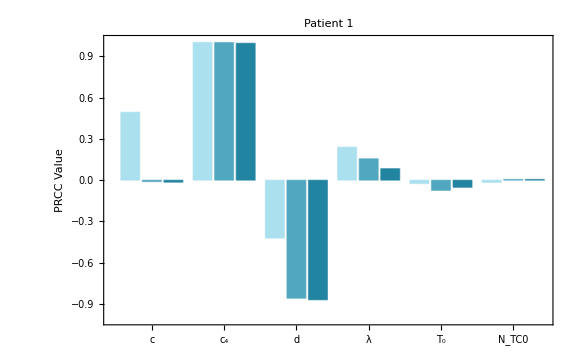

```mathematica
PRCCparm={"c","c_4","d","λ","T_0","N_TC0"};
If[Length[LHSMatrix]==Length[AP1T24],PRCC2[LHSMatrix,AP1T24,AP1T111,AP1T146,PRCCparm,"Patient 1",24,4,5,6],Print["ALERT: LHS Matrix and Y vector are not the same length"]]
```

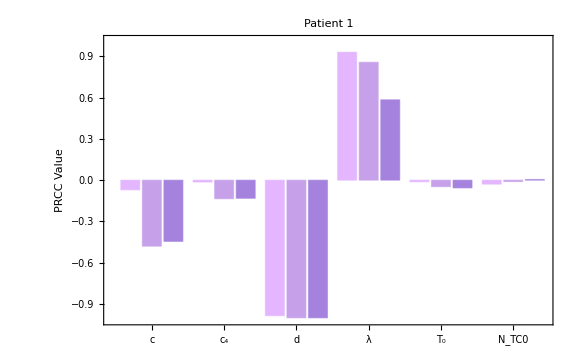

```mathematica
PRCCparm={"c","c_4","d","λ","T_0","N_TC0"};
If[Length[LHSMatrix]==Length[TuP1T24],PRCC2[LHSMatrix,TuP1T24,TuP1T111,TuP1T146,PRCCparm,"Patient 1",55,7,9,10],Print["ALERT: LHS Matrix and Y vector are not the same length"]]
```

#### Patient 2

```mathematica
AbsoluteTiming[
Do[Export[ToString[i]<>"P2SAs.mx",{Flatten[Transpose[Yvec[i,2,2,1000.,1]],1],Flatten[Transpose[Yvec[i,2,2,1000.,2]],1]}],{i,{21,111,146}}]]
```

{6452.24,Null}

```mathematica
P2T24=Import["21P2SAs.mx"];
P2T111=Import["111P2SAs.mx"];
P2T146=Import["146P2SAs.mx"];
```

```mathematica
AP2T24=P2T24[[1]];
AP2T111=P2T111[[1]];
AP2T146=P2T146[[1]];
TuP2T24=P2T24[[2]];
TuP2T111=P2T111[[2]];
TuP2T146=P2T146[[2]];
```

```mathematica
Length[AP2T24]
```

1000

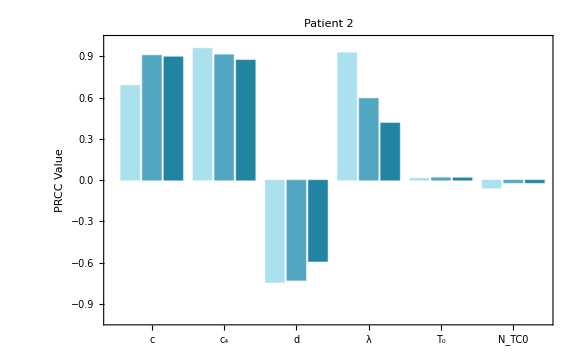

```mathematica
PRCCparm={"c","c_4","d","λ","T_0","N_TC0"};
If[Length[LHSMatrix]==Length[AP2T24],PRCC2[LHSMatrix,AP2T24,AP2T111,AP2T146,PRCCparm,"Patient 2",24,4,5,6],Print["ALERT: LHS Matrix and Y vector are not the same length"]]
```

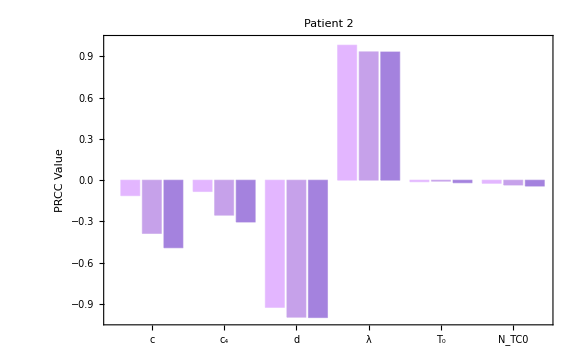

```mathematica
PRCCparm={"c","c_4","d","λ","T_0","N_TC0"};
If[Length[LHSMatrix]==Length[TuP2T24],PRCC2[LHSMatrix,TuP2T24,TuP2T111,TuP2T146,PRCCparm,"Patient 2",55,7,9,10],Print["ALERT: LHS Matrix and Y vector are not the same length"]]
```

#### Patient 3

```mathematica
AbsoluteTiming[
Do[Export[ToString[i]<>"P3SAs.mx",{Flatten[Transpose[Yvec[i,3,3,1000,1]],1],Flatten[Transpose[Yvec[i,3,3,1000,2]],1]}],{i,{21,111,146}}]]
```

{0.352339,Null}

```mathematica
P3T24=Import["21P3SAs.mx"];
P3T111=Import["111P3SAs.mx"];
P3T146=Import["146P3SAs.mx"];
```

```mathematica
AP3T24=P3T24[[1]];
AP3T111=P3T111[[1]];
AP3T146=P3T146[[1]];
TuP3T24=P3T24[[2]];
TuP3T111=P3T111[[2]];
TuP3T146=P3T146[[2]];
```

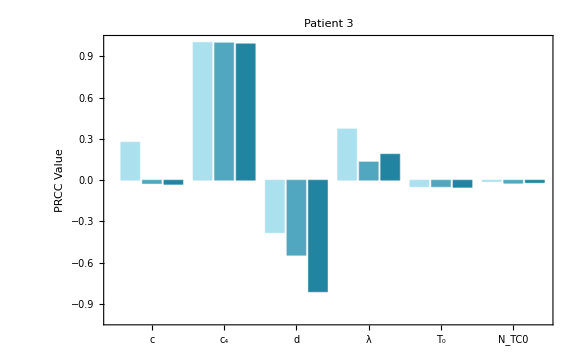

```mathematica
PRCCparm={"c","c_4","d","λ","T_0","N_TC0"};
If[Length[LHSMatrix]==Length[AP3T24],PRCC2[LHSMatrix,AP3T24,AP3T111,AP3T146,PRCCparm,"Patient 3",24,4,5,6],Print["ALERT: LHS Matrix and Y vector are not the same length"]]
```

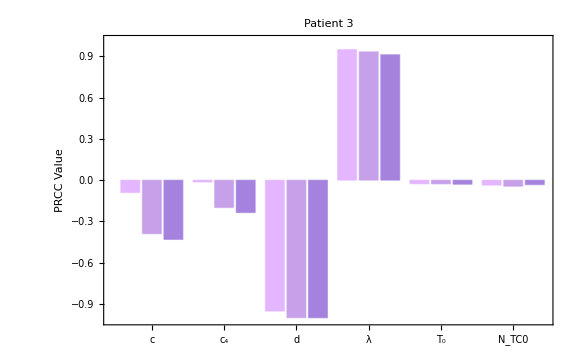

```mathematica
PRCCparm={"c","c_4","d","λ","T_0","N_TC0"};
If[Length[LHSMatrix]==Length[TuP3T24],PRCC2[LHSMatrix,TuP3T24,TuP3T111,TuP3T146,PRCCparm,"Patient 3",55,7,9,10],Print["ALERT: LHS Matrix and Y vector are not the same length"]]
```

#### Patient 4

```mathematica
AbsoluteTiming[
Do[Export[ToString[i]<>"P4SAs.mx",{Flatten[Transpose[Yvec[i,4,4,1000,1]],1],Flatten[Transpose[Yvec[i,4,4,1000,2]],1]}],{i,{21,111,146}}]]
```

{1148.57,Null}

```mathematica
P4T24=Import["21P4SAs.mx"];
P4T111=Import["111P4SAs.mx"];
P4T146=Import["146P4SAs.mx"];
```

```mathematica
AP4T24=P4T24[[1]];
AP4T111=P4T111[[1]];
AP4T146=P4T146[[1]];
TuP4T24=P4T24[[2]];
TuP4T111=P4T111[[2]];
TuP4T146=P4T146[[2]];
```

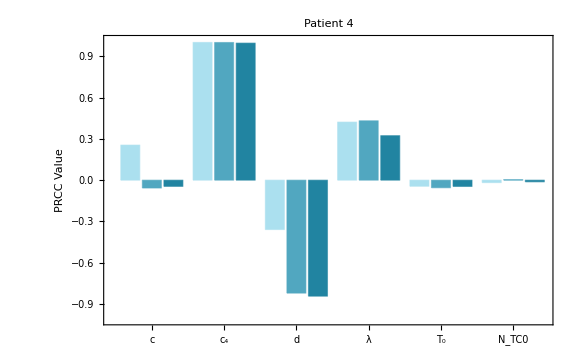

```mathematica
PRCCparm={"c","c_4","d","λ","T_0","N_TC0"};
If[Length[LHSMatrix]==Length[AP4T24],PRCC2[LHSMatrix,AP4T24,AP4T111,AP4T146,PRCCparm,"Patient 4",24,4,5,6],Print["ALERT: LHS Matrix and Y vector are not the same length"]]
```

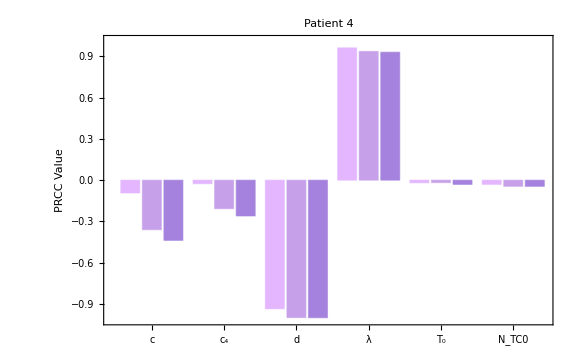

```mathematica
PRCCparm={"c","c_4","d","λ","T_0","N_TC0"};
If[Length[LHSMatrix]==Length[TuP4T24],PRCC2[LHSMatrix,TuP4T24,TuP4T111,TuP4T146,PRCCparm,"Patient 4",55,7,9,10],Print["ALERT: LHS Matrix and Y vector are not the same length"]]
```

#### Patient 5

```mathematica
AbsoluteTiming[
Do[Export[ToString[i]<>"P5SAs.mx",{Flatten[Transpose[Yvec[i,5,5,1000,1]],1],Flatten[Transpose[Yvec[i,5,5,1000,2]],1]}],{i,{21,111,146}}]]
```

{2655.64,Null}

```mathematica
P5T24=Import["21P5SAs.mx"];
P5T111=Import["111P5SAs.mx"];
P5T146=Import["146P5SAs.mx"];
```

```mathematica
AP5T24=P5T24[[1]];
AP5T111=P5T111[[1]];
AP5T146=P5T146[[1]];
TuP5T24=P5T24[[2]];
TuP5T111=P5T111[[2]];
TuP5T146=P5T146[[2]];
```

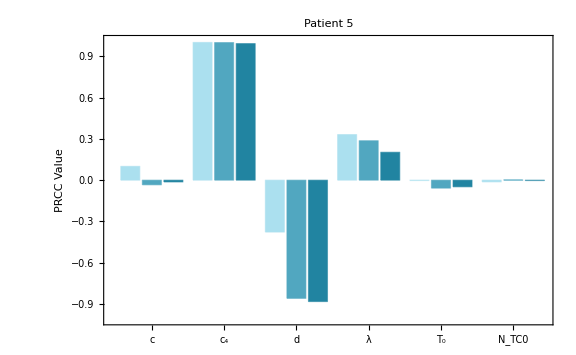

```mathematica
PRCCparm={"c","c_4","d","λ","T_0","N_TC0"};
If[Length[LHSMatrix]==Length[AP5T24],PRCC2[LHSMatrix,AP5T24,AP5T111,AP5T146,PRCCparm,"Patient 5",24,4,5,6],Print["ALERT: LHS Matrix and Y vector are not the same length"]]
```

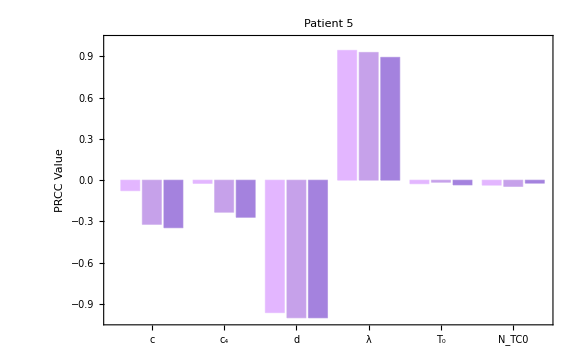

```mathematica
PRCCparm={"c","c_4","d","λ","T_0","N_TC0"};
If[Length[LHSMatrix]==Length[TuP5T24],PRCC2[LHSMatrix,TuP5T24,TuP5T111,TuP5T146,PRCCparm,"Patient 5",55,7,9,10],Print["ALERT: LHS Matrix and Y vector are not the same length"]]
```

#### Patient 6

```mathematica
AbsoluteTiming[
Do[Export[ToString[i]<>"P6SAs.mx",{Flatten[Transpose[Yvec[i,6,6,1000,1]],1],Flatten[Transpose[Yvec[i,6,6,1000.,2]],1]}],{i,{21,111,146}}]]
```

{0.0426526,Null}

```mathematica
P6T24=Import["21P6SAs.mx"];
P6T111=Import["111P6SAs.mx"];
P6T146=Import["146P6SAs.mx"];
```

```mathematica
AP6T24=P6T24[[1]];
AP6T111=P6T111[[1]];
AP6T146=P6T146[[1]];
TuP6T24=P6T24[[2]];
TuP6T111=P6T111[[2]];
TuP6T146=P6T146[[2]];
```

```mathematica
Length[AP6T24]
```

1000

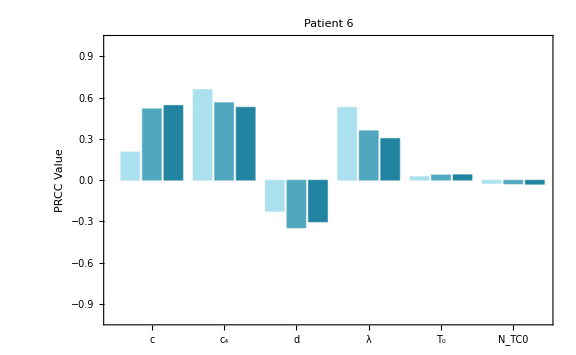

```mathematica
PRCCparm={"c","c_4","d","λ","T_0","N_TC0"};
If[Length[LHSMatrix]==Length[AP6T24],PRCC2[LHSMatrix,AP6T24,AP6T111,AP6T146,PRCCparm,"Patient 6",24,4,5,6],Print["ALERT: LHS Matrix and Y vector are not the same length"]]
```

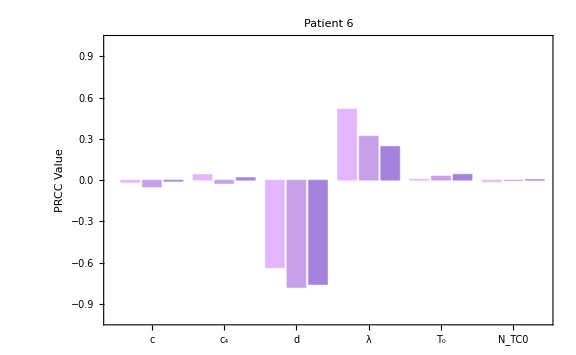

```mathematica
PRCCparm={"c","c_4","d","λ","T_0","N_TC0"};
If[Length[LHSMatrix]==Length[TuP6T24],PRCC2[LHSMatrix,TuP6T24,TuP6T111,TuP6T146,PRCCparm,"Patient 6",55,7,9,10],Print["ALERT: LHS Matrix and Y vector are not the same length"]]
```